1. Trafikflöde

a) Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt?
Antagandet är felaktigt för x_1=0 och x_2=200 eftersom det till x_1 anslutna flödet ut (40) ej är anslutet till x_2.

b) Vilka andra förenklingar har vi antagit?
Enligt antagandet så måste x_1 leda ut i 3 olika flöden vilket endast kan förklaras med en 3 filig rondell där ingen motsatt trafik eller andra störningar äger rum.

b) Ställ upp ekvationssystemet.

```mathematica
200==Subscript[x, 1]+Subscript[x, 2];
100==Subscript[x, 2]+Subscript[x, 3]-Subscript[x, 5];
60==Subscript[x, 5]+Subscript[x, 4];
40==Subscript[x, 1]-Subscript[x, 3]-Subscript[x, 4];
Piecewise[{{200==Subscript[x, 1]+Subscript[x, 2], □}, {100==Subscript[x, 2]+Subscript[x, 3]-Subscript[x, 5], □}, {60==Subscript[x, 5]+Subscript[x, 4], □}, {40==Subscript[x, 1]-Subscript[x, 3]-Subscript[x, 4], □}}]
```

c) Bestäm trafikflödet för vägsystemet.
Trafikflödet har flera heltalslösningar inom ett intervall för varje variabel.

```mathematica
NumberLinePlot[{Subscript[x, 1]-Subscript[x, 3]-Subscript[x, 4]==40,Subscript[x, 1]+Subscript[x, 2]==200,Subscript[x, 2]+Subscript[x, 3]-Subscript[x, 5]==100,Subscript[x, 4]+Subscript[x, 5]==60},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5]}]
```

-Graphics-

Hur ändras trafikflödet om  x_4 är noll ?
Om x_4=0 så måste x_5=60 för att flödet 60(ut) ska uppfyllas. Eftersom x_1 fortfarande kan tilldela x_5 så är detta den ända skillnaden. Tillåtna värden för x_1 är 40 ≤ x ≤ 200 och tillåtna värden på x_2 är 0 ≤ x_2 ≤ 160.

e) Antag att trafiken måste flyta i de riktningar som anges i figuren. Om x_4 är noll vad är då minsta värdet på x_1?
Om x_4=0 så måste x_1 ≥ 40 eftersom att flödet 40(ut) ändå måste uppfyllas.

2. Kaniner

a) Beräkna talföljden och rita en graf över den.
Värdet av ett specifikt tal i talföljden är summan av de två föregående värdena i talföljden. Detta kan beskrivas med hjälp av rekursion:
p_n=p_(n-1)+p_(n-2) där n är det utvalda talet i talföljden.

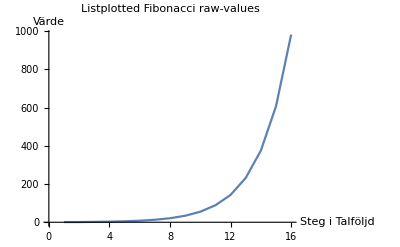

```mathematica
l1=List[1,1,2,3,5,8,13,21,34,55,89,143,232,375,607,982];
ListPlot[l1, Joined->True, AxesLabel->{"Steg i Talföljd","Värde"},PlotLabel->"Listplotted Fibonacci raw-values"]
```

Ovan finns en lista med uträknade “råa” värden baserat på Fibonacci. Listan illustreras via funktionen “ListPlot” och för att länka samman punkterna so används argumentet “Joined”.

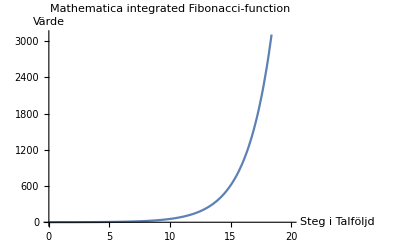

```mathematica
Plot[Fibonacci[n],{n,0,20},AxesLabel->{"Steg i Talföljd","Värde"},PlotLabel ->"Mathematica integrated Fibonacci-function"]
```

Ovan illustreras Fibonaccis talföljd via Mathematicas inbyggda funktion “Fibonacci[ ]”.

-Graphics-

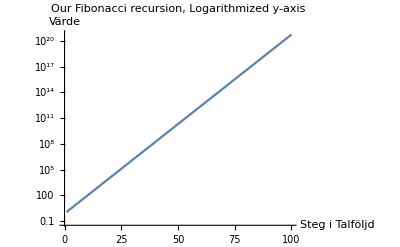

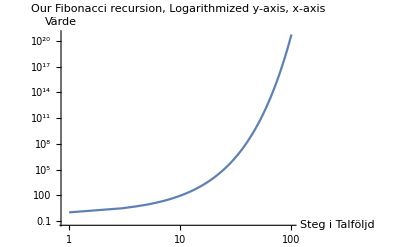

```mathematica
f[x_]:=f[x]=f[x-1]+f[x-2];
f[0]=f[1]=1;
ListPlot[Array[f,100], Joined->True,AxesLabel->{"Steg i Talföljd","Värde"},PlotLabel->"Our Fibonacci recursion"]
ListLogPlot[Array[f,100], Joined->True,AxesLabel->{"Steg i Talföljd","Värde"},PlotLabel->"Our Fibonacci recursion, Logarithmized y-axis"]
ListLogLogPlot[Array[f,100], Joined->True,AxesLabel->{"Steg i Talföljd","Värde"},PlotLabel->"Our Fibonacci recursion, Logarithmized y-axis, x-axis"]
```

Ovan defineras först en rekursiv fuktion på Fibonaccis talföljd. Två startvärden tilldelas värdet 1. Genom funktionen “Array” skapas en lista baserat på den angivna funktionens värden som sedan illustreras genom “ListPlot”, “ListLogPlot”, “ListLogLogPlot”.

b) Undersök talföljden och diskutera tillväxtakten.
Tillväxten är exponentiell. Genom att betrakta talföjden så noteras en ökning för varje steg av summan av de två föregående värden i talföljden. För att talföljden ska vara giltig så initieras 1 som startvärde. Om det inte finns något värde innan 0 så kommer talföljden också få värdet 0 enligt dess definition(0+0=0...). Enligt antagandet så startar man med ett kaninpar som ej är könsmogna och därför återkommer värdet 1 i andra steget. Vid andra steget är kaninerna könsmogna och förökar sig därför till nästa steg 3(värde 2, ett könsmoget par och ett par ungar). I steg 4 så finns 2 könsmogna par men varav endast ett av paren har hunnit få ungar(värde 3, 2 par vuxna kaniner och 1 par ungar).

c) Vilka begränsningar har modellen?
1. Kaniner får inte dö.
2. Det uppstår inga genetiska problem vid inavel.
3. Det föds varje månad en unge per könsmogen kanin.
4. Det finns endast ett kaninpar vid månad n = 1. 
d) Hur kan man förbättra modellen?

KÄLLOR:
http://umu.diva-portal.org/smash/get/diva2:479176/FULLTEXT01.pdf